# Projet Final du IFT 6141 -- Reconnaissance des formes Introduction de l’algorithme Apriori Étudiant: Zhibin Lu le 19 déc. 2017

## 1.Démonstration 2.Analyse un ensemble de données réel.

## 1. Démonstration Ensemble de transaction:

```mathematica
data1=
{{"TID","Item1","Item2","Item3","Item4","Item5"},
{"100","Vin","Fromage","Chocolat"},
{"200","Baguette","Fromage","Croissant"},
{"300","Vin","Baguette","Fromage","Croissant"},
{"400","Baguette","Croissant"}};
TableView[data1,FieldSize->{{1.,8.},{1.,1.}}]
```

TIDItem1Item2Item3Item4Item5100VinFromageChocolat200BaguetteFromageCroissant300VinBaguetteFromageCroissant400BaguetteCroissantNullNullNullNullNullNullNullNullNullNullNullNullNullNullNullNullNullNullNullNullNullNullNullNullNullNullNullNullNullNullNullNullNullNullNullNullNullNullNullNullNull

```mathematica
data1=
{{"Vin","Fromage","Chocolat"},
{"Baguette","Fromage","Croissant"},
{"Vin","Baguette","Fromage","Croissant"},
{"Baguette","Croissant"}};
```

```mathematica
(* Import l'algorithme Apriori *)
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/AprioriAlgorithm.m"]
```

## Obtenir tous les ensembles d'items frequent EIF dont valeur de support > 0.5, c-t-d la probabilte de frequence >0.001

```mathematica
(* AprioriApplication[setOfItemSets,minProb,opts] returns a list of three elements:association sets with indexes,item to indexes rules,and indexes to item rules.The association sets appear in setOfItemSets with frequency that is at least minProb. Option "MaxNumberOfItems"->All/1/2/3 *)
{d1assSets,d1item2ind,d1ind2item}=AprioriApplication[data1,0.5,"MaxNumberOfItems"->All];
```

```mathematica
(*items -> indices*)
(*d1ind=data1/.d1item2ind*)
data1
showdata=d1ind/.d1ind2item

Print["tous les EIF >0.5:",Length[d1assSets]]
(*ensemble d'itmes frequent, EIF L1*)
Print["Tous les L1:"]
d1assSets[[1]]/.d1ind2item

(*EIF L2*)
Print["Tous les L2:"]
d1assSets[[2]]/.d1ind2item

(*EIF L3*)
Print["Tous les L3:"]
d1assSets[[3]]/.d1ind2item

(*EIF L4*)
(*Print["Tous les L4:"]
d1assSets[[4]]/.d1ind2item*)
```

{{Vin,Fromage,Chocolat},{Baguette,Fromage,Croissant},{Vin,Baguette,Fromage,Croissant},{Baguette,Croissant}}

{{Vin,Fromage,Chocolat},{Baguette,Fromage,Croissant},{Vin,Baguette,Fromage,Croissant},{Baguette,Croissant}}

tous les EIF >0.5:3

Tous les L1:

{{Baguette},{Croissant},{Fromage},{Vin}}

Tous les L2:

{{Baguette,Croissant},{Baguette,Fromage},{Croissant,Fromage},{Fromage,Vin}}

Tous les L3:

{{Baguette,Croissant,Fromage}}

## calculer les valeurs de support selon les EIFs

```mathematica
L1supportSets={};
For[j=1,j≤Length[d1assSets[[1]]],j++,
L1supportSets=Append[L1supportSets,{Support[data1,d1assSets[[1,j]]/.d1ind2item]*Length[data1],d1assSets[[1,j]]/.d1ind2item}];
]
L2supportSets={};
For[j=1,j≤Length[d1assSets[[2]]],j++,
L2supportSets=Append[L2supportSets,{Support[data1,d1assSets[[2,j]]/.d1ind2item]*Length[data1],d1assSets[[2,j]]/.d1ind2item}];
]
L3supportSets={};
For[j=1,j≤Length[d1assSets[[3]]],j++,
L3supportSets=Append[L3supportSets,{Support[data1,d1assSets[[3,j]]/.d1ind2item]*Length[data1],d1assSets[[3,j]]/.d1ind2item}];
]
(*
L4supportSets={};
For[j=1,j≤Length[d1assSets[[4]]],j++,
L4supportSets=Append[L4supportSets,{Support[data1,d1assSets[[4,j]]/.d1ind2item]*Length[data1],d1assSets[[4,j]]/.d1ind2item}];
]*)
```

L1:{{3,{Baguette}},{3,{Croissant}},{3,{Fromage}},{2,{Vin}}}

L2:{{3,{Baguette,Croissant}},{2,{Baguette,Fromage}},{2,{Croissant,Fromage}},{2,{Fromage,Vin}}}

L3:{{2,{Baguette,Croissant,Fromage}}}

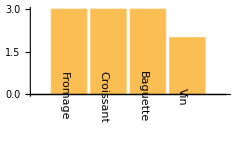

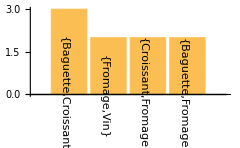

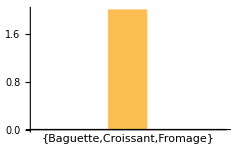

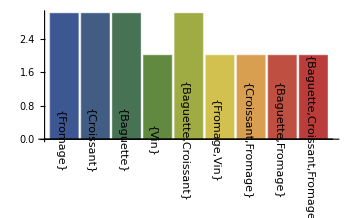

```mathematica
Print["L1:",L1supportSets];
Print["L2:",L2supportSets];
Print["L3:",L3supportSets];
topL1=Reverse[SortBy[L1supportSets,First]];
BarChart[topL1[[All,1]],ChartLabels->(Rotate[ #,3 Pi/2]&/@topL1[[All,2,1]])]
topL2=Reverse[SortBy[L2supportSets,First]];
BarChart[topL2[[All,1]],ChartLabels->(Rotate[#,3 Pi/2]&/@topL2[[All,2]])]
topL3=Reverse[SortBy[L3supportSets,First]];
BarChart[topL3[[All,1]],ChartLabels->Placed[ topL3[[All,2]],Below]]
topL=Join[Join[topL1[[All,1]],topL2[[All,1]]],topL3[[All,1]]];
topLlable=Join[Join[topL1[[All,2]],topL2[[All,2]]],topL3[[All,2]]];
BarChart[topL,ChartLabels->(Rotate[#,3 Pi/2]&/@topLlable),ChartStyle->"DarkRainbow"]
(*topL4=Reverse[SortBy[L4supportSets,First]];
BarChart[topL4[[All,1]],ChartLabels->(Rotate[#,3 Pi/2]&/@topL4[[All,2]])]
*)
```

## Trouver les regles d’association fortes

```mathematica
(* trouver les règles fortes sur L2, confiance>=0.5 *)
assRules2={};
For[i=1,i≤Length[d1assSets[[2]]],i++,
assRules2=Append[assRules2,AssociationRules[data1/.d1item2ind,d1assSets[[2,i]],0.5]/.d1ind2item]
]
assRulesChart={};
assRulesLabel={};
For[i=1,i≤Length[assRules2],i++,
For[j=1,j≤Length[assRules2[[i]]],j++,
Print[assRules2[[i,j,6]],"->",assRules2[[i,j,7]] ,"=",assRules2[[i,j,2]],", ",assRules2[[i,j,1]]];
assRulesChart=Append[assRulesChart,assRules2[[i,j,2]]];
assRulesLabel=Append[assRulesLabel,assRules2[[i,j,6]]<>" -> "<>assRules2[[i,j,7]]];
]
]
(*BarChart[assRulesChart,ChartLabels->(Rotate[#,3 Pi/2]&/@assRulesLabel),ChartStyle->"DarkRainbow"]*)
```

{Baguette}->{Croissant}=1., 0.75

{Croissant}->{Baguette}=1., 0.75

{Baguette}->{Fromage}=0.666667, 0.5

{Fromage}->{Baguette}=0.666667, 0.5

{Croissant}->{Fromage}=0.666667, 0.5

{Fromage}->{Croissant}=0.666667, 0.5

{Vin}->{Fromage}=1., 0.5

{Fromage}->{Vin}=0.666667, 0.5

{Baguette,Fromage}->{Croissant}=1.   Support:0.5

{Croissant,Fromage}->{Baguette}=1.   Support:0.5

{Fromage}->{Baguette,Croissant}=0.666667   Support:0.5

{Baguette,Croissant}->{Fromage}=0.666667   Support:0.5

{Baguette}->{Croissant,Fromage}=0.666667   Support:0.5

{Croissant}->{Baguette,Fromage}=0.666667   Support:0.5

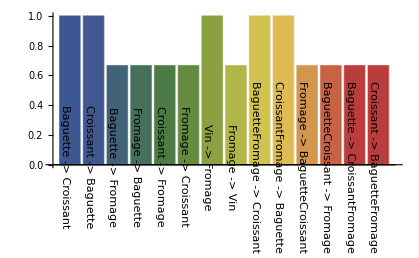

```mathematica
(* trouver les règles fortes sur L3, >0.5 *)
assRules3={};
For[i=1,i≤Length[d1assSets[[3]]],i++,
assRules3=Append[assRules3,AssociationRules[data1/.d1item2ind,d1assSets[[3,i]],0.5]/.d1ind2item]
]
assRules3PourChart={{"Règle","Confiance"}};
For[i=1,i≤Length[assRules3],i++,
For[j=1,j≤Length[assRules3[[i]]],j++,
assRules3PourChart=Append[assRules3PourChart,{ToString[assRules3[[i,j,6]]]<>"->"<>ToString[assRules3[[i,j,7]]],assRules3[[i,j,2]],assRules3[[i,j,1]]}];
Print[assRules3[[i,j,6]],"->",assRules3[[i,j,7]] ,"=",assRules3[[i,j,2]],"   Support:",assRules3[[i,j,1]]];
assRulesChart=Append[assRulesChart,assRules3[[i,j,2]]];
assRulesLabel=Append[assRulesLabel,assRules3[[i,j,6]]<>" -> "<>assRules3[[i,j,7]]];
]
]
assRules3PourChart;
BarChart[assRulesChart,ChartLabels->(Rotate[#,3 Pi/2]&/@assRulesLabel),ChartStyle->"DarkRainbow"]
```

```mathematica
(* AssociationRules[setOfItemSets,assocItemSet,minConfidence]finds the possible association rules for assocItemSet using setOfItemSets that have confidence at least minConfidence and calculates for each of the rules the measures:Support,Confidence,Lift,Leverage,and Conviction.AssociationRules[setOfItemSets,assocItemSets,minConfidence,minSupport] takes the association sets from assocItemSets that have support at least minSupport and finds the association rules for them. *)
tt={"Fromage","Vin","Chocolat"}
tt2={"Fromage","Viande"}
AssociationRules[d1ind,tt/.d1item2ind,0.4]/.d1ind2item
AssociationRules[d1ind,{tt/.d1item2ind,tt2/.d1item2ind},0.1,0.1]/.d1ind2item
```

{Fromage,Vin,Chocolat}

{Fromage,Viande}

{{0.333333,0.666667,0.8,-0.0833333,0.5,{Chocolat,Fromage},{Vin}},{0.333333,0.666667,1.,0.,1.,{Chocolat,Vin},{Fromage}},{0.333333,0.666667,1.,0.,1.,{Fromage,Vin},{Chocolat}},{0.333333,0.5,1.,0.,1.,{Chocolat},{Fromage,Vin}},{0.333333,0.5,1.,0.,1.,{Fromage},{Chocolat,Vin}},{0.333333,0.4,0.8,-0.0833333,0.833333,{Vin},{Chocolat,Fromage}}}

{{0.333333,0.666667,0.8,-0.0833333,0.5,{Chocolat,Fromage},{Vin}},{0.333333,0.666667,1.,0.,1.,{Chocolat,Vin},{Fromage}},{0.333333,0.666667,1.,0.,1.,{Fromage,Vin},{Chocolat}},{0.333333,0.5,1.,0.,1.,{Chocolat},{Fromage,Vin}},{0.333333,0.5,1.,0.,1.,{Fromage},{Chocolat,Vin}},{0.333333,0.4,0.8,-0.0833333,0.833333,{Vin},{Chocolat,Fromage}},{0.333333,1.,1.5,0.111111,1000.,{Viande},{Fromage}},{0.333333,0.5,1.5,0.111111,1.33333,{Fromage},{Viande}}}

```mathematica
(* Support[setOfItemSets,itemSet] gives the fraction of the sets in setOfItemSets that contain itemSet.*)
Support[data1,{"Chocolat","Fromage","Vin"}]//N
```

0.333333

```mathematica
(* ItemRules[setOfItemSets,frequentSetsOfIDs,itemToIDRules,idToItemRules,itemSpec,minConfidence,minSupport,nAssocItems]\
finds rules for a specified item or list if items using the baskets data and the result of AprioriApplication.*)
ItemRules[data1,{{{"Chocolat"},{"Fromage"},{"Vin"}},{{"Chocolat","Vin"}}}/.d1item2ind,d1item2ind,d1ind2item,{"Chocolat","Fromage","Vin"},0.1,0.1,All]
```

{}

## 2.Analyse un ensemble de données réel. Un ensemble de données comprend les listes de catégories de 77,185 places aux États-Unis. Chaque ligne correspond à la liste de catégories d’un lieu, où la liste est constituée d’un certain nombre d’instances de catégorie. Par exemple, hôtels, restaurants, etc. Un exemple de ligne est fourni ci-dessous : “Hôtels et voyages”, “Arts et divertissements”, “Casinos”, “Services et planification d’événements”, “Hôtels”. Dans l’exemple ci-dessus, l’endroit correspondant à cinq instances de catégorie : “Hôtels”, “Casinos”, etc. Maintenant, On va analyser cet ensemble de données en utilisant l’approche d’Apriori.

```mathematica
SetDirectory["./"];
data=ReadList["Projet-apriori-data.txt",Record,RecordLists->True];
data5={};
For[i=1,i≤Length[data],i++,
 data5=Append[data5,StringSplit[data[[i]],";"][[1]] ];
];
```

```mathematica
Dimensions[data5]
data5[[10]]
```

{77185}

{Automotive,Windshield Installation & Repair,Auto Detailing,Wheel & Rim Repair}

## Obtenir les ensembles d’items frequent EIF avec support ≥ 0.01

```mathematica
{d5assSets,d5item2ind,d5ind2item}=AprioriApplication[data5,0.01];
```

```mathematica
Print["tous les EIF > 0.01:",Length[d5assSets]]
(* EIF L1*)
Print["Tous les L1 > 0.01:"]
d5assSets[[1]]/.d5ind2item

(* EIF L2*)
Print["Tous les L2 > 0.01:"]
d5assSets[[2]]/.d5ind2item

(*EIF L3*)
Print["Tous les L3 > 0.01:"]
d5assSets[[3]]/.d5ind2item
```

tous les EIF > 0.01:3

Tous les L1 > 0.01:

{{Active Life},{American (New)},{American (Traditional)},{Arts & Entertainment},{Automotive},{Auto Repair},{Bakeries},{Bars},{Beauty & Spas},{Breakfast & Brunch},{Burgers},{Cafes},{Chinese},{Coffee & Tea},{Dentists},{Doctors},{Event Planning & Services},{Fashion},{Fast Food},{Financial Services},{Fitness & Instruction},{Food},{General Dentistry},{Grocery},{Hair Salons},{Health & Medical},{Home & Garden},{Home Services},{Hotels},{Hotels & Travel},{Ice Cream & Frozen Yogurt},{Italian},{Japanese},{Local Services},{Mexican},{Nail Salons},{Nightlife},{Pets},{Pet Services},{Pizza},{Professional Services},{Pubs},{Real Estate},{Restaurants},{Sandwiches},{Shopping},{Specialty Food},{Sports Bars},{Sushi Bars},{Women's Clothing}}

Tous les L2 > 0.01:

{{Active Life,Fitness & Instruction},{American (New),Restaurants},{American (Traditional),Restaurants},{Automotive,Auto Repair},{Bakeries,Food},{Bars,Nightlife},{Bars,Pubs},{Bars,Restaurants},{Bars,Sports Bars},{Beauty & Spas,Hair Salons},{Beauty & Spas,Nail Salons},{Breakfast & Brunch,Restaurants},{Burgers,Fast Food},{Burgers,Restaurants},{Cafes,Restaurants},{Chinese,Restaurants},{Coffee & Tea,Food},{Dentists,General Dentistry},{Dentists,Health & Medical},{Doctors,Health & Medical},{Event Planning & Services,Hotels},{Event Planning & Services,Hotels & Travel},{Fashion,Shopping},{Fashion,Women's Clothing},{Fast Food,Restaurants},{Food,Grocery},{Food,Ice Cream & Frozen Yogurt},{Food,Restaurants},{Food,Specialty Food},{General Dentistry,Health & Medical},{Home & Garden,Shopping},{Home Services,Real Estate},{Hotels,Hotels & Travel},{Italian,Restaurants},{Japanese,Restaurants},{Mexican,Restaurants},{Nightlife,Pubs},{Nightlife,Restaurants},{Nightlife,Sports Bars},{Pets,Pet Services},{Pizza,Restaurants},{Restaurants,Sandwiches},{Restaurants,Sushi Bars},{Shopping,Women's Clothing}}

Tous les L3 > 0.01:

{{Bars,Nightlife,Pubs},{Bars,Nightlife,Restaurants},{Bars,Nightlife,Sports Bars},{Burgers,Fast Food,Restaurants},{Dentists,General Dentistry,Health & Medical},{Event Planning & Services,Hotels,Hotels & Travel},{Fashion,Shopping,Women's Clothing}}

## Calculer les valeurs de support selon les EIF

```mathematica
L1supportSets={};
For[j=1,j≤Length[d5assSets[[1]]],j++,
L1supportSets=Append[L1supportSets,{Support[data5,d5assSets[[1,j]]/.d5ind2item]*Length[data5],d5assSets[[1,j]]/.d5ind2item}];
]
L2supportSets={};
For[j=1,j≤Length[d5assSets[[2]]],j++,
L2supportSets=Append[L2supportSets,{Support[data5,d5assSets[[2,j]]/.d5ind2item]*Length[data5],d5assSets[[2,j]]/.d5ind2item}];
]
L3supportSets={};
For[j=1,j≤Length[d5assSets[[3]]],j++,
L3supportSets=Append[L3supportSets,{Support[data5,d5assSets[[3,j]]/.d5ind2item]*Length[data5],d5assSets[[3,j]]/.d5ind2item}];
]
```

```mathematica
Reverse[SortBy[L3supportSets,First]]
```

{{2423,{Bars,Nightlife,Restaurants}},{1431,{Event Planning & Services,Hotels,Hotels & Travel}},{1138,{Fashion,Shopping,Women's Clothing}},{874,{Bars,Nightlife,Pubs}},{823,{Dentists,General Dentistry,Health & Medical}},{818,{Bars,Nightlife,Sports Bars}},{774,{Burgers,Fast Food,Restaurants}}}

Nombre de L1:50

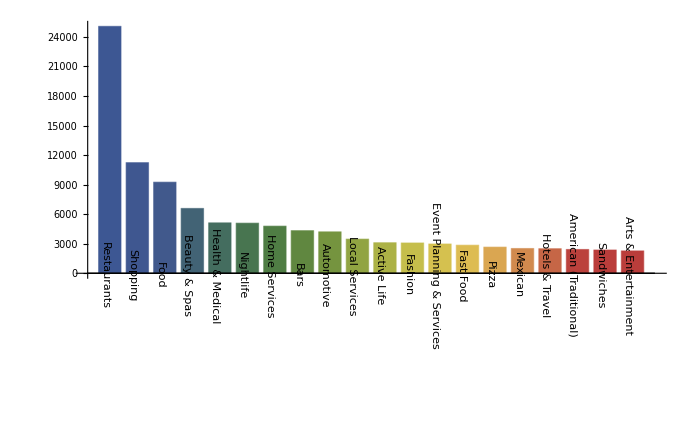

```mathematica
Print["Nombre de L1:",Length[L1supportSets]]
topL1=Reverse[SortBy[L1supportSets,First]][[1;;20]];
BarChart[topL1[[All,1]],ChartLabels->(Rotate[ #,3 Pi/2]&/@topL1[[All,2,1]]),ChartStyle->"DarkRainbow"]
```

Nombre de L1:44

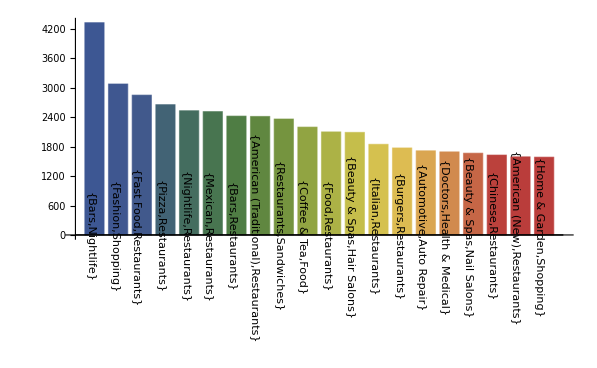

```mathematica
Print["Nombre de L1:",Length[L2supportSets]]
topL2=Reverse[SortBy[L2supportSets,First]][[1;;20]];
BarChart[topL2[[All,1]],ChartLabels->(Rotate[ #,3 Pi/2]&/@topL2[[All,2]]),ChartStyle->"DarkRainbow"]
```

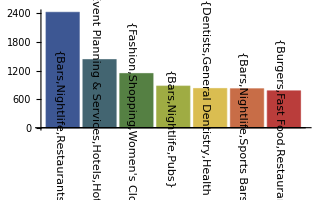

```mathematica
topL3=Reverse[SortBy[L3supportSets,First]];
BarChart[topL3[[All,1]],ChartLabels->(Rotate[ #,3Pi/2]&/@topL3[[All,2]]),ChartStyle->"DarkRainbow"]
```

## Trouver les règles d' association fortes

```mathematica
(* trouver les regles d' association fortes sur L2, >0.8 *)
assRules2={};
For[i=1,i≤Length[d5assSets[[2]]],i++,
assRules2=Append[assRules2,AssociationRules[data5/.d5item2ind,d5assSets[[2,i]],0.8]/.d5ind2item]
]
assRulesChart={};
assRulesLabel={};
For[i=1,i≤Length[assRules2],i++,
For[j=1,j≤Length[assRules2[[i]]],j++,
Print[assRules2[[i,j,6]],"->",assRules2[[i,j,7]] ,"=",assRules2[[i,j,2]],", ",assRules2[[i,j,1]]];
assRulesChart=Append[assRulesChart,assRules2[[i,j,2]]];
assRulesLabel=Append[assRulesLabel,assRules2[[i,j,6]]<>" -> "<>assRules2[[i,j,7]]];
]
]
```

{Fitness & Instruction}->{Active Life}=1., 0.0186824

{American (New)}->{Restaurants}=1., 0.0206387

{American (Traditional)}->{Restaurants}=1., 0.0313014

{Auto Repair}->{Automotive}=1., 0.0222323

{Bakeries}->{Food}=1., 0.0144458

{Bars}->{Nightlife}=1., 0.0560731

{Nightlife}->{Bars}=0.850629, 0.0560731

{Pubs}->{Bars}=1., 0.0113234

{Sports Bars}->{Bars}=1., 0.0105979

{Hair Salons}->{Beauty & Spas}=1., 0.0270908

{Nail Salons}->{Beauty & Spas}=1., 0.0215975

{Breakfast & Brunch}->{Restaurants}=1., 0.0177366

{Burgers}->{Restaurants}=1., 0.0229837

{Cafes}->{Restaurants}=1., 0.0129818

{Chinese}->{Restaurants}=1., 0.0211051

{Coffee & Tea}->{Food}=1., 0.02849

{General Dentistry}->{Dentists}=1., 0.0106627

{Dentists}->{Health & Medical}=1., 0.0154823

{Doctors}->{Health & Medical}=1., 0.0219473

{Hotels}->{Event Planning & Services}=1., 0.0185399

{Fashion}->{Shopping}=1., 0.0398782

{Women's Clothing}->{Fashion}=1., 0.0147438

{Fast Food}->{Restaurants}=1., 0.0369372

{Grocery}->{Food}=1., 0.0184492

{Ice Cream & Frozen Yogurt}->{Food}=1., 0.0131891

{Specialty Food}->{Food}=1., 0.0148993

{General Dentistry}->{Health & Medical}=1., 0.0106627

{Home & Garden}->{Shopping}=1., 0.020548

{Real Estate}->{Home Services}=1., 0.0184492

{Hotels}->{Hotels & Travel}=1., 0.0185399

{Italian}->{Restaurants}=1., 0.0239425

{Japanese}->{Restaurants}=1., 0.0109866

{Mexican}->{Restaurants}=1., 0.0325841

{Pubs}->{Nightlife}=1., 0.0113234

{Sports Bars}->{Nightlife}=1., 0.0105979

{Pet Services}->{Pets}=1., 0.0112716

{Pizza}->{Restaurants}=1., 0.0344238

{Sandwiches}->{Restaurants}=1., 0.0306277

{Sushi Bars}->{Restaurants}=1., 0.0103388

{Women's Clothing}->{Shopping}=1., 0.0147438

{Bars,Pubs}->{Nightlife}=1.   Support:0.0113234

{Pubs}->{Bars,Nightlife}=1.   Support:0.0113234

{Nightlife,Pubs}->{Bars}=1.   Support:0.0113234

{Bars,Restaurants}->{Nightlife}=1.   Support:0.0313921

{Nightlife,Restaurants}->{Bars}=0.956573   Support:0.0313921

{Bars,Sports Bars}->{Nightlife}=1.   Support:0.0105979

{Sports Bars}->{Bars,Nightlife}=1.   Support:0.0105979

{Nightlife,Sports Bars}->{Bars}=1.   Support:0.0105979

{Burgers,Fast Food}->{Restaurants}=1.   Support:0.0100279

{Dentists,General Dentistry}->{Health & Medical}=1.   Support:0.0106627

{General Dentistry}->{Dentists,Health & Medical}=1.   Support:0.0106627

{General Dentistry,Health & Medical}->{Dentists}=1.   Support:0.0106627

{Hotels,Hotels & Travel}->{Event Planning & Services}=1.   Support:0.0185399

{Event Planning & Services,Hotels}->{Hotels & Travel}=1.   Support:0.0185399

{Hotels}->{Event Planning & Services,Hotels & Travel}=1.   Support:0.0185399

{Event Planning & Services,Hotels & Travel}->{Hotels}=0.972808   Support:0.0185399

{Fashion,Women's Clothing}->{Shopping}=1.   Support:0.0147438

{Women's Clothing}->{Fashion,Shopping}=1.   Support:0.0147438

{Shopping,Women's Clothing}->{Fashion}=1.   Support:0.0147438

Tous les règles d' association fortes:59

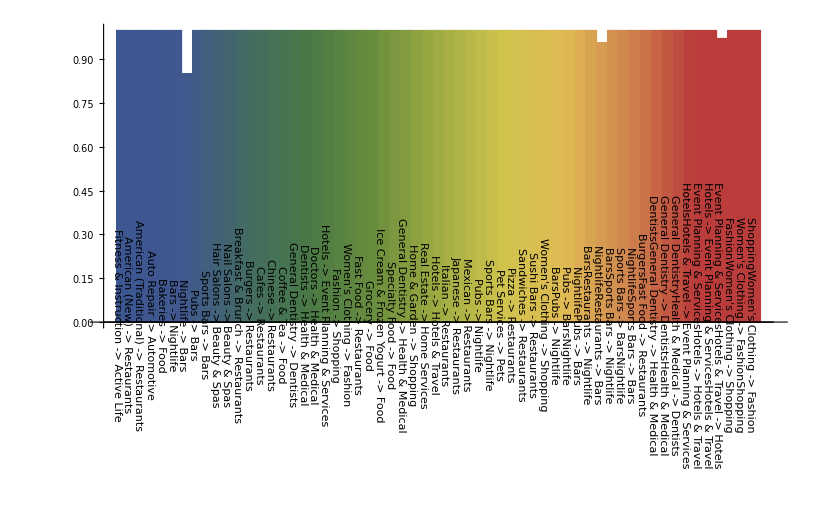

```mathematica
(* trouver les association rules forte sur L3, >0.7 *)
assRules3={};
For[i=1,i≤Length[d5assSets[[3]]],i++,
assRules3=Append[assRules3,AssociationRules[data5/.d5item2ind,d5assSets[[3,i]],0.7]/.d5ind2item]
]

For[i=1,i≤Length[assRules3],i++,
For[j=1,j≤Length[assRules3[[i]]],j++,
Print[assRules3[[i,j,6]],"->",assRules3[[i,j,7]] ,"=",assRules3[[i,j,2]],"   Support:",assRules3[[i,j,1]]];
assRulesChart=Append[assRulesChart,assRules3[[i,j,2]]];assRulesLabel=Append[assRulesLabel,assRules3[[i,j,6]]<>" -> "<>assRules3[[i,j,7]]];
]
]
Print["Tous les règles d' association fortes:",Length[assRulesChart]]
BarChart[assRulesChart,ChartLabels->(Rotate[#,3 Pi/2]&/@assRulesLabel),ChartStyle->"DarkRainbow"]
```

## Conclusion : On remarque que l’approche d’Apriori est très utile pour les affaire de transaction, pour trouver les règles d’association qu’on ne sait pas, pour améliorer l’expérience de client, etc. L’inconvénient majeur de cet algorithme est le nombre considérable de l’accès à la base de données T, un algorithme variant AprioriTid a amélioré ce problème. Pour comparer par les autres algorithmes, il est difficile de lui servir à faire la classification, ou faire une régression. Par exemple on sait seulement « si fromage alors baguette » par Apriori, mais on ne sait pas la relation entre le nombre du fromage et baguette.

RÉFÉRENCES
[1]	Hana Romdhane,Hajer Trabelsi, “Les algorithmes de génération des règles d’association,” 2014. 
[2]	Eng Lian Hu, “Pattern Discovery in Data Mining Programming Assignment: Frequent Itemset Mining Using Apriori” , University of Illinois at Urbana-Champaign, 2016-09-22.
[3]	Hassen M’zali, “Les règles d’Association Séquentielles ”, HEC Montréal, Avril 2006 
[4]	Antononcube, https://github.com/antononcube/MathematicaForPrediction/blob/master/AprioriAlgorithm.m